# Electronic Energy Levels of H_2^+-like Atomic Dimers

```mathematica
SetDirectory[NotebookDirectory[]];
<<diatomic_base.m;
```

## Calculate energy E/Z^2==-2(p/(Z R))^2 in dependence of Z R

```mathematica
CalcP[{l_,m_},pstart_,ZR_List]:=Module[{p0=pstart},{#,p0=FindRoot[RadialPZero[{l,m,p},{2 #,0(*homonuclear*)},10],{p,p0}]⟦1,2⟧}&/@ZR]
```

```mathematica
CalcE[lm_,pstart_,ZR_List]:={First[#],-2(Last[#]/First[#])^2}&/@CalcP[lm,pstart,ZR]
```

```mathematica
CalcErepul[lm_,pstart_,ZR_List]:={First[#],-2(Last[#]/First[#])^2+1/First[#]}&/@CalcP[lm,pstart,ZR]
```

```mathematica
(* Use energy limit E/Z^2==-2(p/(Z R))^2->-1/(2 n^2) for R->∞ as starting point *)
```

```mathematica
ZRrange=Prepend[Exp[Range[Log[0.05],Log[32],0.1]],0];
```

### -2(p/(Z R))^2→-1/(2 1^2) for R→∞

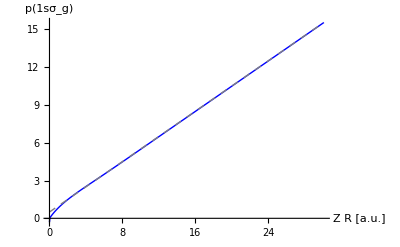

```mathematica
p1sσ=ListPlot[{CalcP[{0,0},(1+Max[ZRrange])/2,Reverse[ZRrange]],{#,(1+#)/2}&/@ZRrange},Joined->True,AxesLabel->{"Z R [a.u.]","p(1sσ_g)"},PlotStyle->{Blue,{Gray,Dashed}}]
```

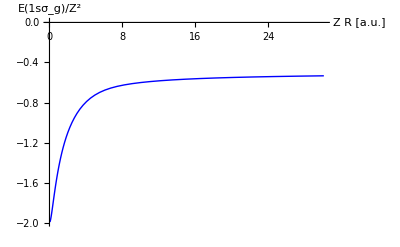

```mathematica
E1sσ=ListPlot[CalcE[{0,0},(1+Max[ZRrange])/2,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(1sσ_g)/Z^2"},AxesOrigin->{0,0},PlotStyle->Blue]
```

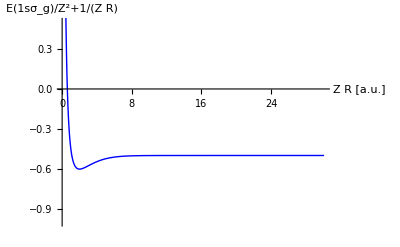

```mathematica
E1sσRepul=ListPlot[CalcErepul[{0,0},(1+Max[ZRrange])/2,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(1sσ_g)/Z^2+1/(Z R)"},AxesOrigin->{0,0},PlotStyle->Blue,PlotRange->{-1,0.5}]
```

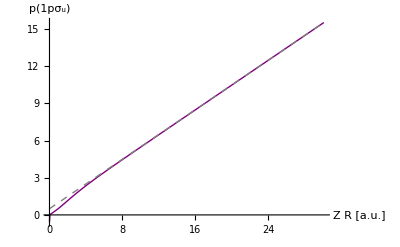

```mathematica
p1pσ=ListPlot[{CalcP[{1,0},(1+Max[ZRrange])/2,Reverse[ZRrange]],{#,(1+#)/2}&/@ZRrange},Joined->True,AxesLabel->{"Z R [a.u.]","p(1pσ_u)"},PlotStyle->{Purple,{Gray,Dashed}}]
```

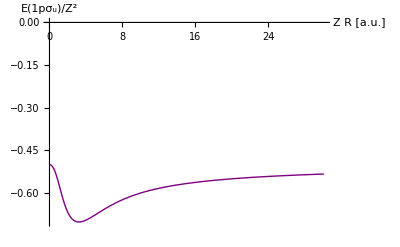

```mathematica
E1pσ=ListPlot[CalcE[{1,0},(1+Max[ZRrange])/2,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(1pσ_u)/Z^2"},AxesOrigin->{0,0},PlotStyle->Purple]
```

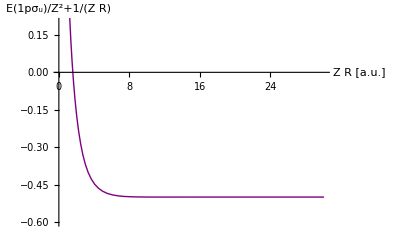

```mathematica
E1pσRepul=ListPlot[CalcErepul[{1,0},(1+Max[ZRrange])/2,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(1pσ_u)/Z^2+1/(Z R)"},AxesOrigin->{0,0},PlotStyle->Purple,PlotRange->{-0.6,0.2}]
```

### -2(p/(Z R))^2→-1/(2 2^2) for R→∞

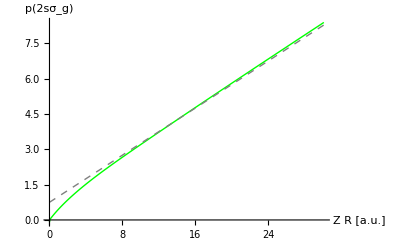

```mathematica
p2sσ=ListPlot[{CalcP[{0,0},(3+Max[ZRrange])/4,Reverse[ZRrange]],{#,(3+#)/4}&/@ZRrange},Joined->True,AxesLabel->{"Z R [a.u.]","p(2sσ_g)"},PlotStyle->{Green,{Gray,Dashed}}]
```

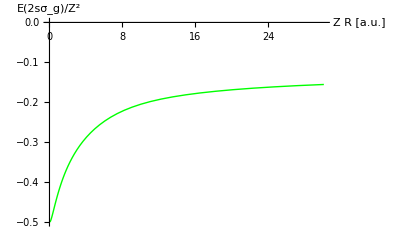

```mathematica
E2sσ=ListPlot[CalcE[{0,0},(3+Max[ZRrange])/4,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(2sσ_g)/Z^2"},AxesOrigin->{0,0},PlotStyle->Green]
```

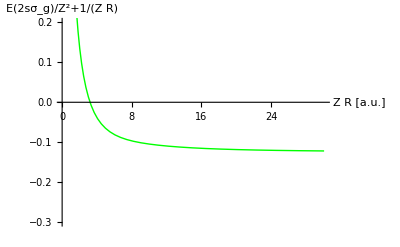

```mathematica
E2sσRepul=ListPlot[CalcErepul[{0,0},(3+Max[ZRrange])/4,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(2sσ_g)/Z^2+1/(Z R)"},AxesOrigin->{0,0},PlotStyle->Green,PlotRange->{-0.3,0.2}]
```

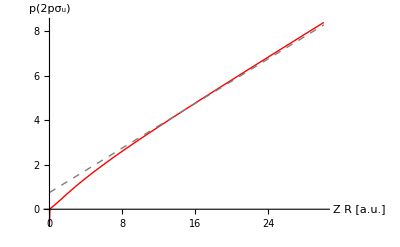

```mathematica
p2pσ=ListPlot[{CalcP[{1,0},(3+Max[ZRrange])/4,Reverse[ZRrange]],{#,(3+#)/4}&/@ZRrange},Joined->True,AxesLabel->{"Z R [a.u.]","p(2pσ_u)"},PlotStyle->{Red,{Gray,Dashed}}]
```

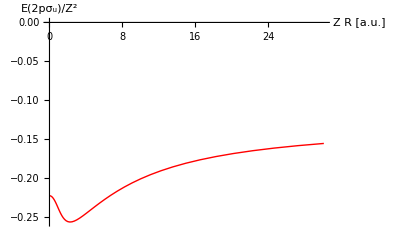

```mathematica
E2pσ=ListPlot[CalcE[{1,0},(3+Max[ZRrange])/4,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(2pσ_u)/Z^2"},AxesOrigin->{0,0},PlotStyle->Red]
```

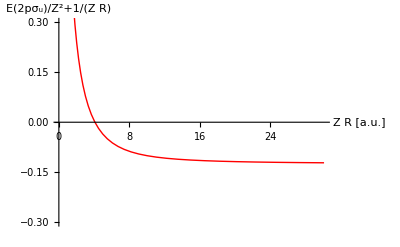

```mathematica
E2pσRepul=ListPlot[CalcErepul[{1,0},(3+Max[ZRrange])/4,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(2pσ_u)/Z^2+1/(Z R)"},AxesOrigin->{0,0},PlotStyle->Red,PlotRange->{-0.3,0.3}]
```

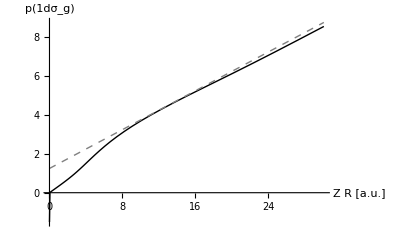

```mathematica
p1dσ=ListPlot[{CalcP[{2,0},(5+Max[ZRrange])/4,Reverse[ZRrange]],{#,(5+#)/4}&/@ZRrange},Joined->True,PlotRange->All,AxesLabel->{"Z R [a.u.]","p(1dσ_g)"},PlotStyle->{Black,{Gray,Dashed}}]
```

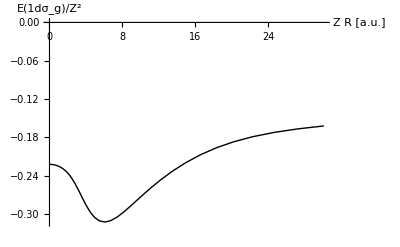

```mathematica
E1dσ=ListPlot[CalcE[{2,0},(5+Max[ZRrange])/4,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(1dσ_g)/Z^2"},AxesOrigin->{0,0},PlotStyle->Black]
```

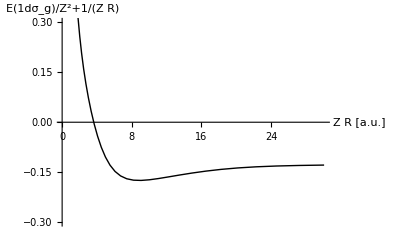

```mathematica
E1dσRepul=ListPlot[CalcErepul[{2,0},(5+Max[ZRrange])/4,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(1dσ_g)/Z^2+1/(Z R)"},AxesOrigin->{0,0},PlotStyle->Black,PlotRange->{-0.3,0.3}]
```

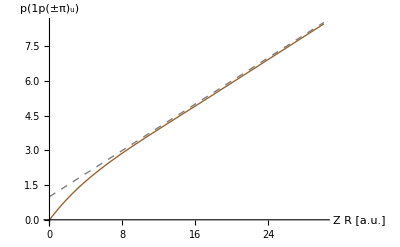

```mathematica
p1pπ=ListPlot[{CalcP[{1,1},(4+Max[ZRrange])/4,Reverse[ZRrange]],{#,(4+#)/4}&/@ZRrange},Joined->True,PlotRange->All,AxesLabel->{"Z R [a.u.]","p(1p(±π)_u)"},PlotStyle->{Brown,{Gray,Dashed}}]
```

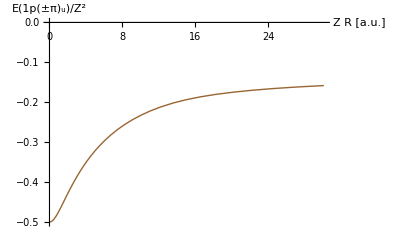

```mathematica
E1pπ=ListPlot[CalcE[{1,1},(4+Max[ZRrange])/4,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(1p(±π)_u)/Z^2"},AxesOrigin->{0,0},PlotStyle->Brown]
```

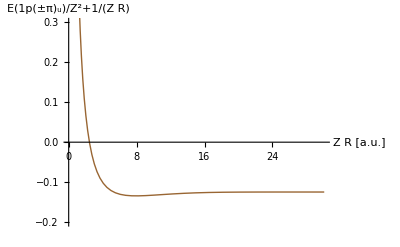

```mathematica
E1pπRepul=ListPlot[CalcErepul[{1,1},(4+Max[ZRrange])/4,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(1p(±π)_u)/Z^2+1/(Z R)"},AxesOrigin->{0,0},PlotStyle->Brown,PlotRange->{-0.2,0.3}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

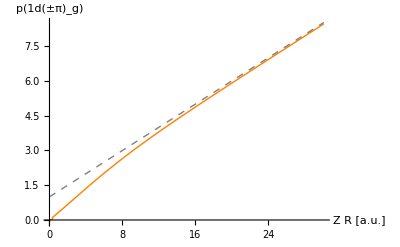

```mathematica
p1dπ=ListPlot[{CalcP[{2,1},(4+Max[ZRrange])/4,Reverse[ZRrange]],{#,(4+#)/4}&/@ZRrange},Joined->True,AxesLabel->{"Z R [a.u.]","p(1d(±π)_g)"},PlotStyle->{Orange,{Gray,Dashed}}]
```

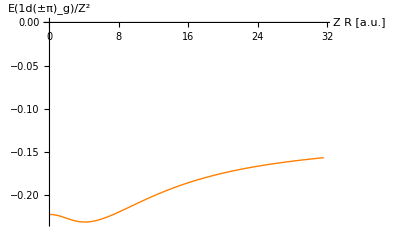

```mathematica
Prepend[Exp[Range[Log[0.05],Log[32],0.05]],0];
E1dπ=ListPlot[CalcE[{2,1},(4+Max[ZRrange])/4,Reverse[Rest[%]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(1d(±π)_g)/Z^2"},AxesOrigin->{0,0},PlotStyle->Orange]
```

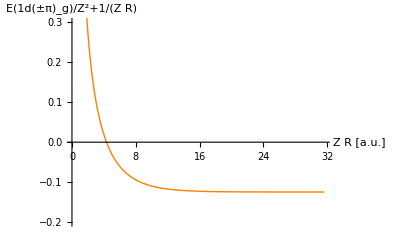

```mathematica
Prepend[Exp[Range[Log[0.05],Log[32],0.05]],0];
E1dπRepul=ListPlot[CalcErepul[{2,1},(4+Max[ZRrange])/4,Reverse[Rest[%]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(1d(±π)_g)/Z^2+1/(Z R)"},AxesOrigin->{0,0},PlotStyle->Orange,PlotRange->{-0.2,0.3}]
```

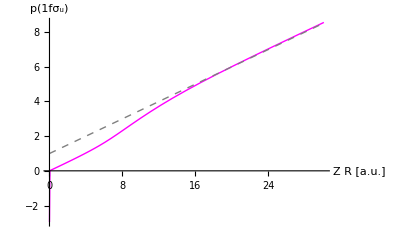

```mathematica
p1fσ=ListPlot[{CalcP[{3,0},(4+Max[ZRrange])/4,Reverse[ZRrange]],{#,(4+#)/4}&/@ZRrange},Joined->True,AxesLabel->{"Z R [a.u.]","p(1fσ_u)"},PlotStyle->{Magenta,{Gray,Dashed}}]
```

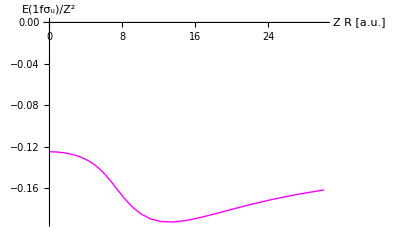

```mathematica
E1fσ=ListPlot[CalcE[{3,0},(4+Max[ZRrange])/4,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(1fσ_u)/Z^2"},AxesOrigin->{0,0},PlotStyle->Magenta]
```

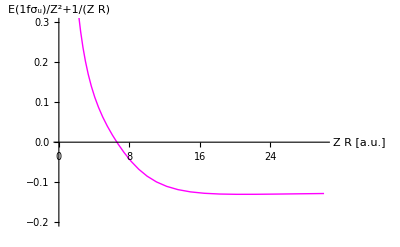

```mathematica
E1fσRepul=ListPlot[CalcErepul[{3,0},(4+Max[ZRrange])/4,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(1fσ_u)/Z^2+1/(Z R)"},AxesOrigin->{0,0},PlotStyle->Magenta,PlotRange->{-0.2,0.3}]
```

### -2(p/(Z R))^2→-1/(2 3^2) for R→∞

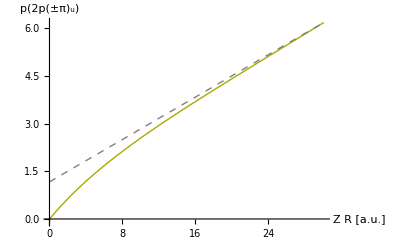

```mathematica
p2pπ=ListPlot[{CalcP[{1,1},(7+Max[ZRrange])/6,Reverse[ZRrange]],{#,(7+#)/6}&/@ZRrange},Joined->True,AxesLabel->{"Z R [a.u.]","p(2p(±π)_u)"},PlotStyle->{Darker[Yellow],{Gray,Dashed}}]
```

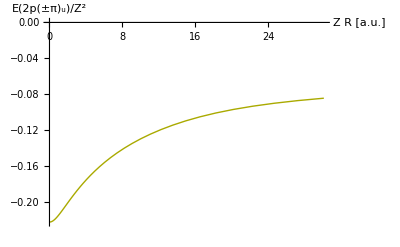

```mathematica
E2pπ=ListPlot[CalcE[{1,1},(7+Max[ZRrange])/6,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(2p(±π)_u)/Z^2"},AxesOrigin->{0,0},PlotStyle->Darker[Yellow]]
```

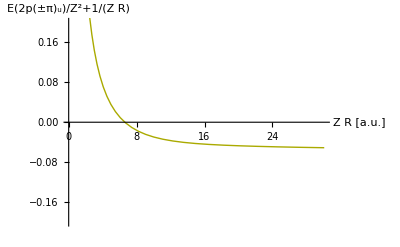

```mathematica
E2pπRepul=ListPlot[CalcErepul[{1,1},(7+Max[ZRrange])/6,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(2p(±π)_u)/Z^2+1/(Z R)"},AxesOrigin->{0,0},PlotStyle->Darker[Yellow],PlotRange->{-0.2,0.2}]
```

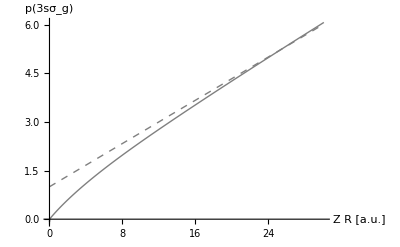

```mathematica
p3sσ=ListPlot[{CalcP[{0,0},(6+Max[ZRrange])/6,Reverse[ZRrange]],{#,(6+#)/6}&/@ZRrange},Joined->True,AxesLabel->{"Z R [a.u.]","p(3sσ_g)"},PlotStyle->{Gray,{Gray,Dashed}}]
```

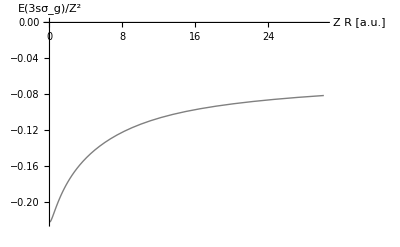

```mathematica
E3sσ=ListPlot[CalcE[{0,0},(6+Max[ZRrange])/6,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(3sσ_g)/Z^2"},AxesOrigin->{0,0},PlotStyle->Gray]
```

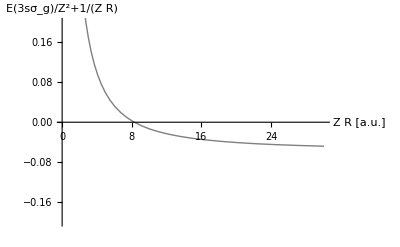

```mathematica
E3sσRepul=ListPlot[CalcErepul[{0,0},(6+Max[ZRrange])/6,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(3sσ_g)/Z^2+1/(Z R)"},AxesOrigin->{0,0},PlotStyle->Gray,PlotRange->{-0.2,0.2}]
```

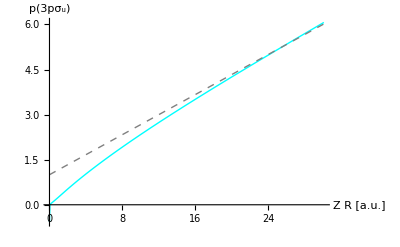

```mathematica
p3pσ=ListPlot[{CalcP[{1,0},(6+Max[ZRrange])/6,Reverse[ZRrange]],{#,(6+#)/6}&/@ZRrange},Joined->True,AxesLabel->{"Z R [a.u.]","p(3pσ_u)"},PlotStyle->{Cyan,{Gray,Dashed}}]
```

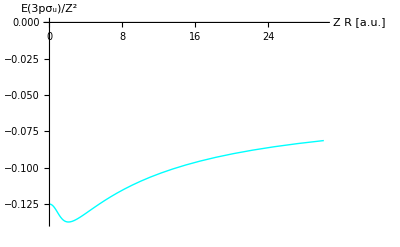

```mathematica
E3pσ=ListPlot[CalcE[{1,0},(6+Max[ZRrange])/6,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(3pσ_u)/Z^2"},AxesOrigin->{0,0},PlotStyle->Cyan]
```

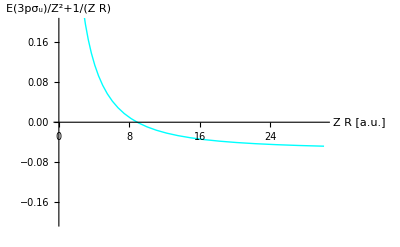

```mathematica
E3pσRepul=ListPlot[CalcErepul[{1,0},(6+Max[ZRrange])/6,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(3pσ_u)/Z^2+1/(Z R)"},AxesOrigin->{0,0},PlotStyle->Cyan,PlotRange->{-0.2,0.2}]
```

### -2(p/(Z R))^2→-1/(2 4^2) for R→∞

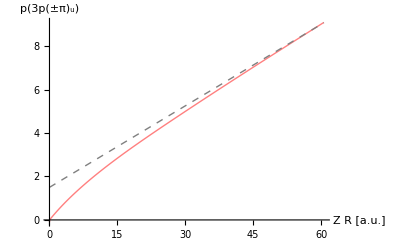

```mathematica
Prepend[Exp[Range[Log[0.05],Log[64],0.1]],0];
p3pπ=ListPlot[{CalcP[{1,1},(12+Max[%])/8,Reverse[%]],{#,(12+#)/8}&/@%},Joined->True,AxesLabel->{"Z R [a.u.]","p(3p(±π)_u)"},PlotStyle->{Pink,{Gray,Dashed}}]
```

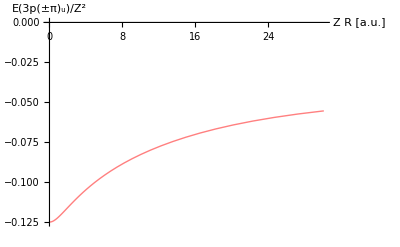

```mathematica
E3pπ=ListPlot[CalcE[{1,1},(12+Max[ZRrange])/8,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(3p(±π)_u)/Z^2"},AxesOrigin->{0,0},PlotStyle->Pink]
```

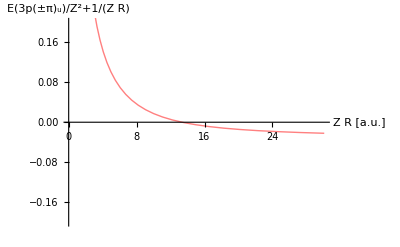

```mathematica
E3pπRepul=ListPlot[CalcErepul[{1,1},(12+Max[ZRrange])/8,Reverse[Rest[ZRrange]]],Joined->True,AxesLabel->{"Z R [a.u.]","E(3p(±π)_u)/Z^2+1/(Z R)"},AxesOrigin->{0,0},PlotStyle->Pink,PlotRange->{-0.2,0.2}]
```

### Assemble plots

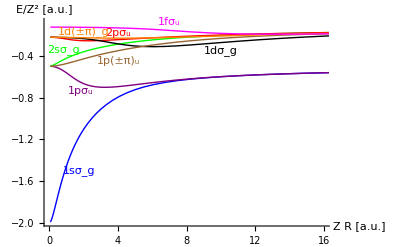

```mathematica
legendplot=Graphics[{Text[Style["1sσ_g",Blue],{1.7,-1.5}],Text[Style["1pσ_u",Purple],{1.8,-0.74}],Text[Style["1p(±π)_u",Brown],{4,-0.45}],Text[Style["2sσ_g",Green],{0.8,-0.34}],Text[Style["2pσ_u",Red],{4,-0.18}],Text[Style["1dσ_g",Black],{10,-0.35}],Text[Style["1d(±π)_g",Orange],{2,-0.17}],Text[Style["1fσ_u",Magenta],{7,-0.08}](*,Text[Style["3sσ_g",Gray],{12,-0.05}],Text[Style["3pσ_u",Cyan],{9,-0.06}]*)}];
Show[E1sσ(*Blue*),E1pσ(*Purple*),E2sσ(*Green*),E2pσ(*Red*),E1dσ(*Black*),E1pπ(*Brown*),E1dπ(*Orange*),E1fσ(*Magenta*)(*,E3sσ(*Gray*),E3pσ(*Cyan*)*),legendplot,PlotRange->{{0,16},All},AxesLabel->{"Z R [a.u.]","E/Z^2 [a.u.]"}]
```

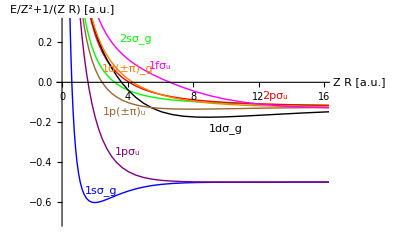

```mathematica
legendplotRepul=Graphics[{Text[Style["1sσ_g",Blue],{2.4,-0.54}],Text[Style["1pσ_u",Purple],{4,-0.35}],Text[Style["1p(±π)_u",Brown],{3.8,-0.15}],Text[Style["2sσ_g",Green],{4.5,0.22}],Text[Style["2pσ_u",Red],{13,-0.07}],Text[Style["1dσ_g",Black],{10,-0.23}],Text[Style["1d(±π)_g",Orange],{4,0.07}],Text[Style["1fσ_u",Magenta],{6,0.08}](*,Text[Style["3sσ_g",Gray],{12,-0.05}],Text[Style["3pσ_u",Cyan],{9,-0.06}]*)}];
Show[E1sσRepul(*Blue*),E1pσRepul(*Purple*),E2sσRepul(*Green*),E2pσRepul(*Red*),E1dσRepul(*Black*),E1pπRepul(*Brown*),E1dπRepul(*Orange*),E1fσRepul(*Magenta*)(*,RepulE3sσRepul(*Gray*),E3pσ(*Cyan*)*),legendplotRepul,PlotRange->{{0,16},{-0.7,0.3}},AxesLabel->{"Z R [a.u.]","E/Z^2+1/(Z R) [a.u.]"}]
```

## Convergence to hydrogen energy levels for R→∞

```mathematica
CalcEDiff[lm_,n_,pstart_,ZR_List]:={First[#],Abs[-2(Last[#]/First[#])^2+1/First[#]+1/(2 n^2)]}&/@CalcP[lm,pstart,ZR]
```

```mathematica
ZRrange=Prepend[Exp[Range[Log[12],Log[200],0.1]],0];
```

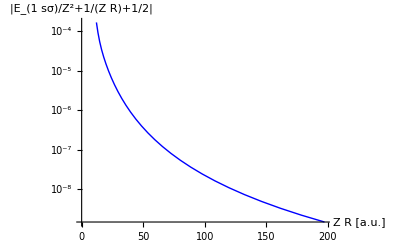

{197.336,1.48388×10^-9}

```mathematica
E1sσDiff=CalcEDiff[{0,0},1,(1+Max[ZRrange])/2,Reverse[Rest[ZRrange]]];
ListLogPlot[E1sσDiff,Joined->True,PlotRange->{{0,E1sσDiff⟦1,1⟧},{E1sσDiff⟦1,2⟧,E1sσDiff⟦-1,2⟧}},PlotStyle->Blue,AxesLabel->{"Z R [a.u.]","|E_(1  sσ)/Z^2+1/(Z R)+1/2|"}]
First[E1sσDiff]
```

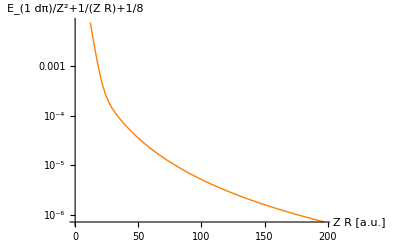

{197.336,7.2939×10^-7}

```mathematica
E1dπDiff=CalcEDiff[{2,1},2,(4+Max[ZRrange])/4,Reverse[Rest[ZRrange]]];
ListLogPlot[E1dπDiff,Joined->True,PlotStyle->Orange,PlotRange->{{0,E1dπDiff⟦1,1⟧},{E1dπDiff⟦1,2⟧,E1dπDiff⟦-1,2⟧}},AxesLabel->{"Z R [a.u.]","E_(1  dπ)/Z^2+1/(Z R)+1/8"}]
First[E1dπDiff]
```

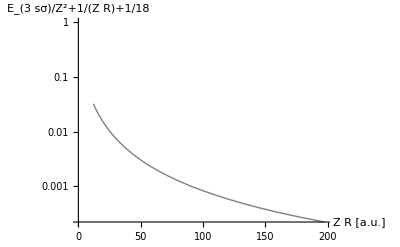

{197.336,0.000221625}

```mathematica
E3sσDiff=CalcEDiff[{0,0},3,(6+Max[ZRrange])/6,Reverse[Rest[ZRrange]]];
ListLogPlot[E3sσDiff,Joined->True,PlotStyle->Gray,AxesLabel->{"Z R [a.u.]","E_(3  sσ)/Z^2+1/(Z R)+1/18"}]
First[E3sσDiff]
```